## NICER J0740 (OLD) -- TG did NOT update this

```mathematica
SetDirectory[NotebookDirectory[]];
fname="../constraints/mrdata/nicer_J0740_original/0740_maryland_nxmm.h5";
Import[fname,"Dimensions"]
Mlist=Import[fname,"m_bins"];
Rlist=Import[fname,"r_bins"];
wList=Import[fname,"weights"];
wmrList=Flatten[Table[{Rlist[[i]],Mlist[[j]],wList[[i,j]]},{i,Length[Rlist]-1},{j,Length[Mlist]-1}],1];
wmrInt=Interpolation[wmrList,InterpolationOrder->1]
DensityPlot[wmrInt[x,y],{x,Rlist[[1]],Rlist[[-1]]},{y,Mlist[[1]],Mlist[[-1]]},PlotPoints->200,PlotRange->All]
wmrInt[13,2]
```

<|/m_bins→{50},/r_bins→{50},/weights→{49,49}|>

InterpolatingFunction[…]

-Graphics-

0.881953

```mathematica
(* regriding constraint data *)
MmidList=Table[(Mlist[[i]]+Mlist[[i+1]])/2,{i,Length[Mlist]-1}];
RmidList=Table[(Rlist[[i]]+Rlist[[i+1]])/2,{i,Length[Rlist]-1}];
wMidList=Flatten[Table[{RmidList[[i]],MmidList[[j]],wList[[i,j]]},{i,Length[RmidList]},{j,Length[MmidList]}],1];
wMidInt=Interpolation[wMidList,InterpolationOrder->1]
wListNew=Table[wMidInt[x,y],{x,Rlist},{y,Mlist}]//Quiet;
wmrList=Flatten[Table[{Rlist[[i]],Mlist[[j]],wListNew[[i,j]]},{i,Length[Rlist]},{j,Length[Mlist]}],1];
wmrInt=Interpolation[wmrList,InterpolationOrder->1]
DensityPlot[wmrInt[x,y],{x,Rlist[[1]],Rlist[[-1]]},{y,Mlist[[1]],Mlist[[-1]]},PlotPoints->200,PlotRange->All]
dM=Mlist[[2]]-Mlist[[1]];
dR=Rlist[[2]]-Rlist[[1]];
wmrInt[13,2]
wmrInt[13+dR/2,2+dM/2]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

-Graphics-

0.823377

0.875701

```mathematica
wMidInt[13,2]
```

0.80964

```mathematica
(* exporting data constrained data file *)
datasets={"m_bins","r_bins","weights"};
dataout={MmidList,RmidList,wList};
Export["0740_maryland_nxmm_regrid2.h5",dataout,{"Datasets",datasets}];
```

```mathematica
{MmidList[[30]],RmidList[[20]],wList[[20,30]]}
```

{1.90306,13.9796,0.119293}

```mathematica
(* exporting data constrained data file *)
datasets={"m_bins","r_bins","weights"};
dataout={Mlist,Rlist,wListNew};
Export["0740_maryland_nxmm_regrid.h5",dataout,{"Datasets",datasets}];
```

```mathematica
(* check *)
fname="0740_maryland_nxmm_regrid.h5";
Import[fname,"Dimensions"]
Mlist=Import[fname,"m_bins"];
Rlist=Import[fname,"r_bins"];
wList=Import[fname,"weights"];
wmrList=Flatten[Table[{Rlist[[i]],Mlist[[j]],wList[[i,j]]},{i,Length[Rlist]},{j,Length[Mlist]}],1];
wmrInt=Interpolation[wmrList,InterpolationOrder->1]
DensityPlot[wmrInt[x,y],{x,Rlist[[1]],Rlist[[-1]]},{y,Mlist[[1]],Mlist[[-1]]},PlotPoints->200,PlotRange->All]
wmrInt[13,2]
```

Import::nffil: File 0740_maryland_nxmm_regrid.h5 not found during Import.

$Failed

Import::nffil: File 0740_maryland_nxmm_regrid.h5 not found during Import.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

Interpolation[{},InterpolationOrder→1]

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

DensityPlot::plln: Limiting value $Failed⟦1⟧ in {x,$Failed⟦1⟧,$Failed⟦-1⟧} is not a machine-sized real number.

DensityPlot[wmrInt[x,y],{x,Rlist⟦1⟧,Rlist⟦-1⟧},{y,Mlist⟦1⟧,Mlist⟦-1⟧},PlotPoints→200,PlotRange→All]

Interpolation[{},InterpolationOrder→1][13,2]

```mathematica
wList[[1,30]]
```

0.000370072

```mathematica
wMidInt[20,2.5]
```

InterpolatingFunction::dmval: Input value {20,2.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.

## NICER J0030 -- TG did NOT update this

```mathematica
SetDirectory[NotebookDirectory[]];
fname="../constraints/mrdata/nicer_J0030/0030_maryland_2spts.h5";
Import[fname,"Dimensions"]
Mlist=Import[fname,"m_bins"];
Rlist=Import[fname,"r_bins"];
wList=Import[fname,"weights"];
wmrList=Flatten[Table[{Rlist[[i]],Mlist[[j]],wList[[i,j]]},{i,Length[Rlist]-1},{j,Length[Mlist]-1}],1];
wmrInt=Interpolation[wmrList,InterpolationOrder->2]
DensityPlot[wmrInt[x,y],{x,Rlist[[1]],Rlist[[-1]]},{y,Mlist[[1]],Mlist[[-1]]},PlotPoints->200,PlotRange->All]
wmrInt[13,1.4]
```

<|/m_bins→{50},/r_bins→{50},/weights→{49,49}|>

InterpolatingFunction[…]

-Graphics-

1.63703

```mathematica
(* regriding constraint data *)
MmidList=Table[(Mlist[[i]]+Mlist[[i+1]])/2,{i,Length[Mlist]-1}];
RmidList=Table[(Rlist[[i]]+Rlist[[i+1]])/2,{i,Length[Rlist]-1}];
wMidList=Flatten[Table[{RmidList[[i]],MmidList[[j]],wList[[i,j]]},{i,Length[RmidList]},{j,Length[MmidList]}],1];
wMidInt=Interpolation[wMidList,InterpolationOrder->1]
wListNew=Table[wMidInt[x,y],{x,Rlist},{y,Mlist}]//Quiet;
wmrList=Flatten[Table[{Rlist[[i]],Mlist[[j]],wListNew[[i,j]]},{i,Length[Rlist]},{j,Length[Mlist]}],1];
wmrInt=Interpolation[wmrList,InterpolationOrder->1]
DensityPlot[wmrInt[x,y],{x,Rlist[[1]],Rlist[[-1]]},{y,Mlist[[1]],Mlist[[-1]]},PlotPoints->200,PlotRange->All]
dM=Mlist[[2]]-Mlist[[1]];
dR=Rlist[[2]]-Rlist[[1]];
wmrInt[13,1.4]
wmrInt[13+dR/2,1.4+dM/2]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

-Graphics-

1.6706

1.61391

13.9796

```mathematica
wMidInt[RmidList[[20]],MmidList[[14]]]
```

0.373096

```mathematica
wMidInt[13,1.4]
```

1.73787

```mathematica
(* exporting data constrained data file *)
datasets={"m_bins","r_bins","weights"};
dataout={MmidList,RmidList,wList};
Export["0030_maryland_2spts_regrid2.h5",dataout,{"Datasets",datasets}];
```

```mathematica
MmidList[[14]]
```

1.41327

```mathematica
(* exporting data constrained data file *)
datasets={"m_bins","r_bins","weights"};
dataout={Mlist,Rlist,wListNew};
Export["0030_maryland_2spts_regrid.h5",dataout,{"Datasets",datasets}];
```

```mathematica
(* check *)
fname="0030_maryland_2spts_regrid.h5";
Import[fname,"Dimensions"]
Mlist=Import[fname,"m_bins"];
Rlist=Import[fname,"r_bins"];
wList=Import[fname,"weights"];
wmrList=Flatten[Table[{Rlist[[i]],Mlist[[j]],wList[[i,j]]},{i,Length[Rlist]},{j,Length[Mlist]}],1];
wmrInt=Interpolation[wmrList,InterpolationOrder->1]
DensityPlot[wmrInt[x,y],{x,Rlist[[1]],Rlist[[-1]]},{y,Mlist[[1]],Mlist[[-1]]},PlotPoints->200,PlotRange->All]
wmrInt[13,1.4]
```

<|/weights→{50,50},/m_bins→{50},/r_bins→{50}|>

InterpolatingFunction[…]

-Graphics-

1.6706

```mathematica
prior[[1,2]]
```

0.0000134835

```mathematica
{L1[[10]],L2[[20]],prInt[L1[[10]],L2[[20]]]}
{L1[[20]],L2[[10]],prInt[L1[[20]],L2[[10]]]}
{100,150,prInt[100,150]}
{150,100,prInt[150,100]}
```

{145.455,307.071,0.000818645}

{307.071,145.455,0.00100896}

{100,150,0.000601934}

{150,100,0.000557451}

0.000818645

## GW170817 data -- TG did NOT update this ; Is this something old that CE didn’t delete?

```mathematica
(* loading Lambda measurements *)
SetDirectory[NotebookDirectory[]];
fname="../constraints/LV/LV_prior.h5";
Import[fname,"Dimensions"]
(* loading Lambda measurements *)
SetDirectory[NotebookDirectory[]];
fname="../constraints/LV/LV_prior.h5";
Import[fname,"Dimensions"]
L1=Import[fname,"x"];
L2=Import[fname,"y"];
prior=Import[fname,"data"];
prList=Flatten[Table[{L1[[i]],L2[[j]],prior[[i,j]]},{i,Length[L1]},{j,Length[L2]}],1];
prInt=Interpolation[prList,InterpolationOrder->1]
DensityPlot[prInt[x,y],{x,L1[[1]],L1[[-1]]},{y,L2[[1]],L2[[-1]]},PlotPoints->200,PlotRange->All]
prInt[200,200]
```

<|/data→{100,100},/x→{100},/y→{100}|>

<|/data→{100,100},/x→{100},/y→{100}|>

InterpolatingFunction[…]

-Graphics-

0.000883328

```mathematica
prior[[10,10]]
```

0.00080355

```mathematica
(* import Lambda data *)
MRL=Import["../build/1.tov","Table"];
```

```mathematica
MRL//Length
```

76691

```mathematica
imax0=28068+2;
imax=imax0;
While[MRL[[imax,1]]<MRL[[imax+1,1]],
Print[imax];
imax+=1;]
```

28070

28071

28072

28073

28074

28075

28076

28077

28078

28079

28080

28081

28082

28083

28084

28085

28086

28087

28088

28089

28090

28091

28092

28093

28094

28095

28096

28097

28098

28099

28100

28101

28102

28103

28104

28105

28106

28107

28108

28109

28110

28111

28112

28113

28114

28115

28116

28117

28118

28119

28120

28121

28122

28123

28124

28125

28126

28127

28128

28129

28130

28131

28132

28133

28134

28135

28136

28137

28138

28139

28140

28141

28142

28143

28144

28145

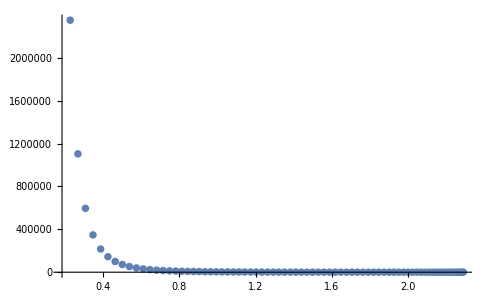

```mathematica
ListPlot[MRL[[imax0;;imax,{1,3}]],PlotRange->All]
```

```mathematica
Lint=Interpolation[MRL[[imax0;;imax,{1,3}]]];
Mmin=1;
Mtov=MRL[[imax,1]]
M1List=Range[Mmin,Mtov,0.01];
M2List=Table[M2/.replM2/.replMc//Evaluate,{M1,M1List}];
L12List=Table[{Lint[M1List[[i]]],Lint[M2List[[i]]]},{i,Length[M1List]}];
(* check *)
Table[Mc[M1List[[i]],M2List[[i]]],{i,Length[M1List]}]
```

2.28804

{1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186,1.186}

```mathematica
p1=DensityPlot[prInt[x,y],{x,L1[[1]],L1[[-1]]},{y,L2[[1]],L2[[-1]]},PlotPoints->200,PlotRange->All]
```

-Graphics-

```mathematica
p2=ListPlot[L12List,Joined->False,PlotStyle->{Red,Thick}]
```

-Graphics-

```mathematica
Show[p1,p2,PlotRange->{{0,1600},{0,1600}}]
```

-Graphics-

```mathematica
(* integrating probability *)
L12int=Interpolation[L12List];
NIntegrate[prInt[l1,L12int[l1]],{l1,20,1600}]
```

0.0837065

```mathematica
89.5
```

89.5

```mathematica
LVdata0=Import["../constraints/LV/low_spin_PhenomPNRT_posterior_samples.dat"];
LVdata0[[1]]
LVdata=LVdata0[[2;;]];
```

{#costheta_jn,luminosity_distance_Mpc,m1_detector_frame_Msun,m2_detector_frame_Msun,lambda1,lambda2,spin1,spin2,costilt1,costilt2}

```mathematica
(* adding sound speed to VQCD tables *)
SetDirectory[NotebookDirectory[]];
EOS1=Import["eosVQCDinterQM.dat"];
(* computing sound speed *)
EOS1int=Interpolation[EOS1,InterpolationOrder->1];
cs2List1=Table[{e,EOS1int'[e]},{e,EOS1[[;;,1]]}];
EOS1cs2=Thread[{EOS1[[;;,1]],EOS1[[;;,2]],cs2List1[[;;,2]]}];
Export["eosVQCDinterQMcs2.dat",EOS1cs2]
```

eosVQCDinterQMcs2.dat

```mathematica
(* adding sound speed to VQCD tables *)
SetDirectory[NotebookDirectory[]];
EOS1=Import["eosVQCDsoftQM.dat"];
(* computing sound speed *)
EOS1int=Interpolation[EOS1,InterpolationOrder->1];
cs2List1=Table[{e,EOS1int'[e]},{e,EOS1[[;;,1]]}];
EOS1cs2=Thread[{EOS1[[;;,1]],EOS1[[;;,2]],cs2List1[[;;,2]]}];
Export["eosVQCDsoftQMcs2.dat",EOS1cs2]
```

eosVQCDsoftQMcs2.dat

```mathematica
(* adding sound speed to VQCD tables *)
SetDirectory[NotebookDirectory[]];
EOS1=Import["eosVQCDstiffQM.dat"];
(* computing sound speed *)
EOS1int=Interpolation[EOS1,InterpolationOrder->1];
cs2List1=Table[{e,EOS1int'[e]},{e,EOS1[[;;,1]]}];
EOS1cs2=Thread[{EOS1[[;;,1]],EOS1[[;;,2]],cs2List1[[;;,2]]}];
Export["eosVQCDstiffQMcs2.dat",EOS1cs2]
```

eosVQCDstiffQMcs2.dat

## UPDATED MR data for J0740 (weight,m,r)

```mathematica
IMPORTDIR="../constraints/mrdata/nicer_J0470_update/";
IMPORTFNAME="J0740_gamma_NxX_lp40k_se001_wmrsamples.dat";
OUTPUTFNAME="J0740_update_regrid_new.h5";
WEIGHTED=True;
LINESTART=2;
```

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import[IMPORTDIR<>IMPORTFNAME][[LINESTART;;]];
If[WEIGHTED,
points=data[[;;,{2,3}]];
weights=data[[;;,1]];
,
points=data[[;;,{1,2}]];
weights=ConstantArray[1,Length@points]
];
dataWeights=WeightedData[points,weights];
```

```mathematica
(* The grid *)
Mmin=Min[points[[;;,1]]];
Mmax=Max[points[[;;,1]]];
Rmin=Min[points[[;;,2]]];
Rmax=Max[points[[;;,2]]];
NM=50;
NR=50;
Rlist=Subdivide[Rmin,Rmax,NR];
Mlist=Subdivide[Mmin,Mmax,NM];
Print[Length/@{Rlist,Mlist}]
```

{51,51}

```mathematica
counts=HistogramList[dataWeights,{{Mlist},{Rlist}}][[-1]];
```

```mathematica
ListPlot3D[counts,InterpolationOrder->0,Filling->Axis,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
(* regriding constraint data *)
MmidList=Table[(Mlist[[i]]+Mlist[[i+1]])/2,{i,Length[Mlist]-1}];
RmidList=Table[(Rlist[[i]]+Rlist[[i+1]])/2,{i,Length[Rlist]-1}];
wMidList=Flatten[Table[{RmidList[[i]],MmidList[[j]],counts[[j,i]]},{i,Length[RmidList]},{j,Length[MmidList]}],1];

(* Want to find the norm now *)
wMidInt=Interpolation[wMidList,InterpolationOrder->1];
norm=NIntegrate[wMidInt[x,y],{x,RmidList[[1]],RmidList[[-1]]},{y,MmidList[[1]],MmidList[[-1]]}];
wMidIntPartition=Table[wMidInt[i,j],{i,RmidList},{j,MmidList}];

DensityPlot[wMidInt[x,y]/norm,{x,RmidList[[1]],RmidList[[-1]]},{y,MmidList[[1]],MmidList[[-1]]},PlotPoints->200,PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00196743 and 1.18322×10^-8 for the integral and error estimates.

-Graphics-

```mathematica
(* exporting data constrained data file *)
datasets={"m_bins","r_bins","weights"};
(* Renormalize the wMidList counts *)
dataout={MmidList,RmidList,wMidIntPartition/norm};
Export[IMPORTDIR<>OUTPUTFNAME,dataout,{"Datasets",datasets}];
```

```mathematica
(* check *)
fname=IMPORTDIR<>OUTPUTFNAME;
Import[fname,"Dimensions"]
Mlist=Import[fname,"m_bins"];
Rlist=Import[fname,"r_bins"];
wList=Import[fname,"weights"];
wmrList=Flatten[Table[{Rlist[[i]],Mlist[[j]],wList[[i,j]]},{i,Length[Rlist]},{j,Length[Mlist]}],1];
ListPlot3D[wmrList,InterpolationOrder->0,Filling->Axis,Mesh->None,PlotRange->All]
```

<|/weights→{50,50},/m_bins→{50},/r_bins→{50}|>

-Graphics3D-

```mathematica
OUTPUTFNAME
```

J0740_regrid_new.h5

```mathematica
(* check the old regridded data *)
fname=IMPORTDIR<>"J0740_update_regrid.h5";
Import[fname,"Dimensions"]
Mlist=Import[fname,"m_bins"];
Rlist=Import[fname,"r_bins"];
wList=Import[fname,"weights"];
wmrList=Flatten[Table[{Rlist[[i]],Mlist[[j]],wList[[i,j]]},{i,Length[Rlist]},{j,Length[Mlist]}],1];
ListPlot3D[wmrList,InterpolationOrder->0,Filling->Axis,Mesh->None,PlotRange->All]
```

<|/m_bins→{50},/r_bins→{50},/weights→{50,50}|>

-Graphics3D-

## MR data for J0437 (m,r)

```mathematica
IMPORTDIR="../constraints/mrdata/nicer_J0437/";
IMPORTFNAME="nlive20000_expf3.3_noCONST_noMM_tol0.1post_equal_weights.dat";
OUTPUTFNAME="J0437_regrid_new.h5";
WEIGHTED=False;
LINESTART=2;
```

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import[IMPORTDIR<>IMPORTFNAME][[LINESTART;;]];
If[WEIGHTED,
points=data[[;;,{2,3}]];
weights=data[[;;,1]];
,
points=data[[;;,{1,2}]];
weights=ConstantArray[1,Length@points]
];
dataWeights=WeightedData[points,weights];
```

```mathematica
(* The grid *)
Mmin=Min[points[[;;,1]]];
Mmax=Max[points[[;;,1]]];
Rmin=Min[points[[;;,2]]];
Rmax=Max[points[[;;,2]]];
NM=50;
NR=50;
Rlist=Subdivide[Rmin,Rmax,NR];
Mlist=Subdivide[Mmin,Mmax,NM];
Print[Length/@{Rlist,Mlist}]
```

{51,51}

```mathematica
counts=HistogramList[dataWeights,{{Mlist},{Rlist}}][[-1]];
```

```mathematica
ListPlot3D[counts,InterpolationOrder->0,Filling->Axis,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
(* regriding constraint data *)
MmidList=Table[(Mlist[[i]]+Mlist[[i+1]])/2,{i,Length[Mlist]-1}];
RmidList=Table[(Rlist[[i]]+Rlist[[i+1]])/2,{i,Length[Rlist]-1}];
wMidList=Flatten[Table[{RmidList[[i]],MmidList[[j]],counts[[j,i]]},{i,Length[RmidList]},{j,Length[MmidList]}],1];

(* Want to find the norm now *)
wMidInt=Interpolation[wMidList,InterpolationOrder->1];
norm=NIntegrate[wMidInt[x,y],{x,RmidList[[1]],RmidList[[-1]]},{y,MmidList[[1]],MmidList[[-1]]}];
wMidIntPartition=Table[wMidInt[i,j],{i,RmidList},{j,MmidList}];

DensityPlot[wMidInt[x,y]/norm,{x,RmidList[[1]],RmidList[[-1]]},{y,MmidList[[1]],MmidList[[-1]]},PlotPoints->200,PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 118.048 and 0.00242049 for the integral and error estimates.

-Graphics-

```mathematica
(* exporting data constrained data file *)
datasets={"m_bins","r_bins","weights"};
(* Renormalize the wMidList counts *)
dataout={MmidList,RmidList,wMidIntPartition/norm};
Export[IMPORTDIR<>OUTPUTFNAME,dataout,{"Datasets",datasets}];
```

```mathematica
(* check *)
fname=IMPORTDIR<>OUTPUTFNAME;
Import[fname,"Dimensions"]
Mlist=Import[fname,"m_bins"];
Rlist=Import[fname,"r_bins"];
wList=Import[fname,"weights"];
wmrList=Flatten[Table[{Rlist[[i]],Mlist[[j]],wList[[i,j]]},{i,Length[Rlist]},{j,Length[Mlist]}],1];
ListPlot3D[wmrList,InterpolationOrder->0,Filling->Axis,Mesh->None,PlotRange->All]
```

<|/weights→{50,50},/m_bins→{50},/r_bins→{50}|>

-Graphics3D-

```mathematica
OUTPUTFNAME
```

J0437_regrid_test.h5

```mathematica
(* check the old regridded data *)
fname=IMPORTDIR<>"J0437_regrid.h5";
Import[fname,"Dimensions"]
Mlist=Import[fname,"m_bins"];
Rlist=Import[fname,"r_bins"];
wList=Import[fname,"weights"];
wmrList=Flatten[Table[{Rlist[[i]],Mlist[[j]],wList[[i,j]]},{i,Length[Rlist]},{j,Length[Mlist]}],1];
ListPlot3D[wmrList,InterpolationOrder->0,Filling->Axis,Mesh->None,PlotRange->All]
```

<|/m_bins→{50},/r_bins→{50},/weights→{50,50}|>

-Graphics3D-

## MR data for J0614 (m,r)

```mathematica
IMPORTDIR="../constraints/mrdata/nicer_J0614/";
IMPORTFNAME="J0614_ST_PDT_20kLP_0p05SE_0p1ET_mrsamples_post_equal_weights.dat";
OUTPUTFNAME="J0614_regrid.h5";
WEIGHTED=False;
LINESTART=1;
```

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import[IMPORTDIR<>IMPORTFNAME][[1;;]];
points=data[[;;,{1,2}]][[LINESTART;;]];
If[WEIGHTED,
weights=data[[;;,3]];,
weights=ConstantArray[1,Length@points];
];
dataWeights=WeightedData[points,weights];
```

```mathematica
(* The grid *)
Mmin=Min[points[[;;,1]]];
Mmax=Max[points[[;;,1]]];
Rmin=Min[points[[;;,2]]];
Rmax=Max[points[[;;,2]]];
NM=50;
NR=50;
Rlist=Subdivide[Rmin,Rmax,NR];
Mlist=Subdivide[Mmin,Mmax,NM];
Print[Length/@{Rlist,Mlist}]
```

{51,51}

```mathematica
counts=HistogramList[dataWeights,{{Mlist},{Rlist}}][[-1]];
```

```mathematica
ListPlot3D[counts,InterpolationOrder->0,Filling->Axis,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
(* regriding constraint data *)
MmidList=Table[(Mlist[[i]]+Mlist[[i+1]])/2,{i,Length[Mlist]-1}];
RmidList=Table[(Rlist[[i]]+Rlist[[i+1]])/2,{i,Length[Rlist]-1}];
wMidList=Flatten[Table[{RmidList[[i]],MmidList[[j]],counts[[j,i]]},{i,Length[RmidList]},{j,Length[MmidList]}],1];

(* Want to find the norm now *)
wMidInt=Interpolation[wMidList,InterpolationOrder->1];
norm=NIntegrate[wMidInt[x,y],{x,RmidList[[1]],RmidList[[-1]]},{y,MmidList[[1]],MmidList[[-1]]}];
wMidIntPartition=Table[wMidInt[i,j],{i,RmidList},{j,MmidList}];

DensityPlot[wMidInt[x,y]/norm,{x,RmidList[[1]],RmidList[[-1]]},{y,MmidList[[1]],MmidList[[-1]]},PlotPoints->200,PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 360.924 and 0.0235182 for the integral and error estimates.

-Graphics-

```mathematica
(* exporting data constrained data file *)
datasets={"m_bins","r_bins","weights"};
(* Renormalize the wMidList counts *)
dataout={MmidList,RmidList,wMidIntPartition/norm};
Export[IMPORTDIR<>OUTPUTFNAME,dataout,{"Datasets",datasets}];
```

```mathematica
(* check *)
fname=IMPORTDIR<>OUTPUTFNAME;
Import[fname,"Dimensions"]
Mlist=Import[fname,"m_bins"];
Rlist=Import[fname,"r_bins"];
wList=Import[fname,"weights"];
wmrList=Flatten[Table[{Rlist[[i]],Mlist[[j]],wList[[i,j]]},{i,Length[Rlist]},{j,Length[Mlist]}],1];
ListDensityPlot[wmrList,PlotRange->All]
```

<|/weights→{50,50},/m_bins→{50},/r_bins→{50}|>

-Graphics-